# Approximation of exponential distribution

## Sampling from an exponential distribution can be approximated as

```mathematica
distMean = 5;
totalDuration = 20 ;
timeStep = 10^(-.4);
```

## Using time step as 1, and matching distribution at t = 0

Appropriate transition probability can be computed as:

```mathematica
Solve[ptr/(1-ptr)==1/(distMean),ptr]
```

{{ptr→1/(1+distMean)}}

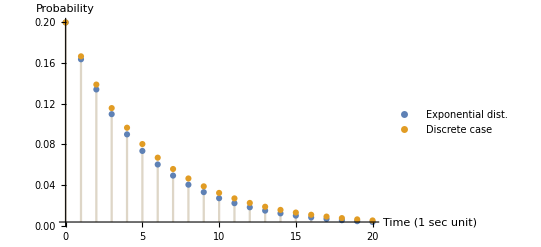

```mathematica
DiscretePlot[{λ Exp[-λ k ]/.{λ-> 1/(distMean)},(1-ptr)^(k-1)* ptr/.Solve[ptr/(1-ptr)==1/(distMean),ptr]},{k,0,20,1},Filling->Axis,PlotRange->All,AxesLabel->{StringForm["Time (`` sec unit)",1],"Probability"},PlotLegends->{"Exponential dist.","Discrete case"}]
```

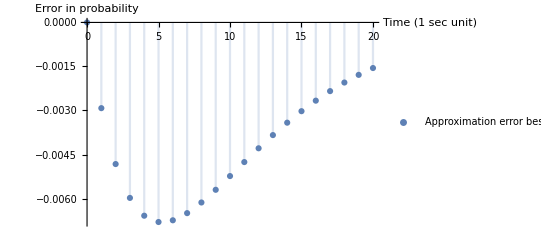

```mathematica
DiscretePlot[{(λ Exp[-λ k ]/.{λ-> 1/(distMean)})-((1-ptr)^(k-1)* ptr/.Solve[ptr/(1-ptr)==1/(distMean),ptr])},{k,0,20,1},Filling->Axis,PlotRange->All,AxesLabel->{StringForm["Time (`` sec unit)",1],"Error in probability"},PlotLegends->{"Approximation error besides binning error"}]
```

## Using time step as 1, and matching distribution at t = 1

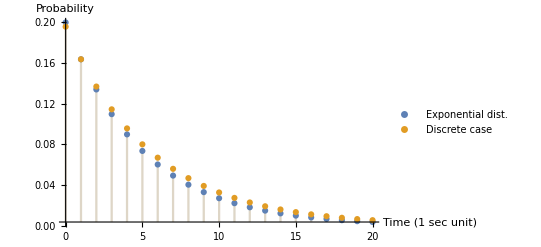

```mathematica
DiscretePlot[{λ Exp[-λ k ]/.{λ-> 1/(distMean)},(1-ptr)^(k-1)* ptr/.{ptr-> λ Exp[-λ  ]}/.{λ-> 1/(distMean)}},{k,0,20,1},Filling->Axis,PlotRange->All,AxesLabel->{StringForm["Time (`` sec unit)",1],"Probability"},PlotLegends->{"Exponential dist.","Discrete case"}]
```

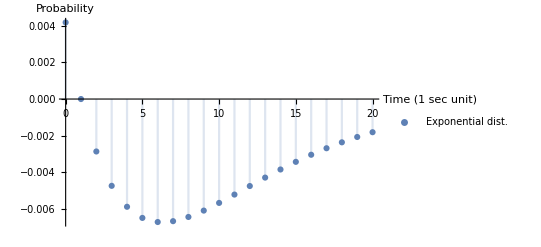

```mathematica
DiscretePlot[{(λ Exp[-λ k ]/.{λ-> 1/(distMean)})-((1-ptr)^(k-1)* ptr/.{ptr-> λ Exp[-λ  ]}/.{λ-> 1/(distMean)})},{k,0,20,1},Filling->Axis,PlotRange->All,AxesLabel->{StringForm["Time (`` sec unit)",1],"Probability"},PlotLegends->{"Exponential dist.","Discrete case"}]
```

## Using time step as ‘timeStep’, and matching distribution at t = 0

Appropriate transition probability can be computed as:

```mathematica
Solve[ptr/(1-ptr)==1/(distMean),ptr]
```

{{ptr→1/(1+distMean)}}

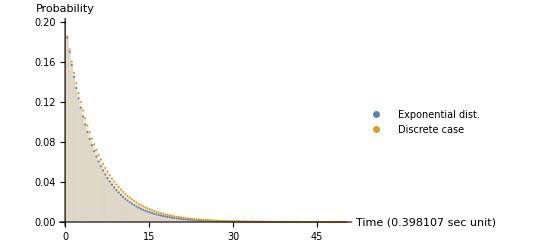

```mathematica
DiscretePlot[{λ Exp[-λ k ]/.{λ-> 1/(distMean)},(1-ptr)^(k-1)* ptr/.Solve[ptr/(1-ptr)==1/(distMean),ptr]},{k, 0,20/timeStep,timeStep},Filling->Axis,PlotRange->All,AxesLabel->{StringForm["Time (`` sec unit)",timeStep],"Probability"},PlotLegends->{"Exponential dist.","Discrete case"}]
```

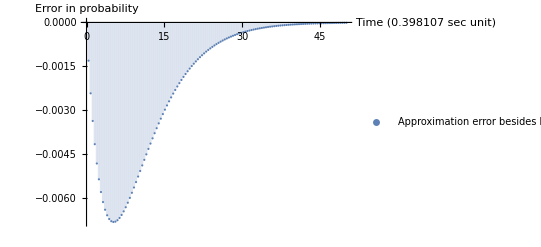

```mathematica
DiscretePlot[(λ Exp[-λ k ]/.{λ-> 1/(distMean)})-((1-ptr)^(k-1)* ptr/.Solve[ptr/(1-ptr)==1/(distMean),ptr]),{k, 0,20/timeStep,timeStep},Filling->Axis,PlotRange->All,AxesLabel->{StringForm["Time (`` sec unit)",timeStep],"Error in probability"},PlotLegends->{"Approximation error besides binning error"}]
```

## Using time step as ‘timeStep’, and matching distribution at t = timeStep (NOT that easy to solve)